```mathematica
powerf[x_,n_,μ_,σ_]:=Module[{a,y},
a=Table[NProbability[y<=x ,Distributed[y,NormalDistribution[μ,σ]]],{i,1,n}];
Times@@a]
```

```mathematica
powerf[494.63,2,499,50]
```

0.216389

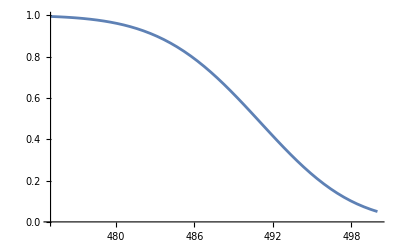

```mathematica
Plot[powerf[494.63,2,μ,Sqrt[50]],{μ,475,500}]
```